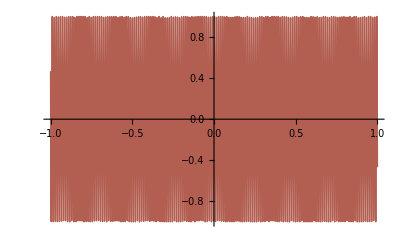

```mathematica
(* zad 1 *)
Plot[Sin[500 x],{x,-1,1},PlotStyle->Thick,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][x^2+y^2]],ColorFunctionScaling->False]
```

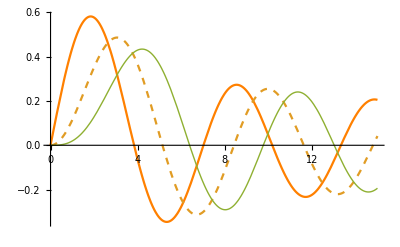

```mathematica
(* zad 2 *)
Plot[Evaluate@Table[BesselJ[n,x],{n,3}],{x,0,15},PlotStyle->{Orange,Dashed,Thick}]
```

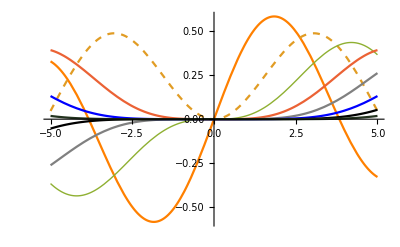

```mathematica
(* zad 3 *)
Plot[Evaluate@Table[BesselJ[n,x],{n,8}],{x,-5,5},PlotStyle->{Orange,Dashed,Thick,Glow,RGBColor[0.5,0.5,0.5],Blue,Black,Hue[0.3,0.4,0.2]}]
```